```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

```mathematica
phiBar[deltaPhi_,T_]:=deltaPhi/T;
```

```mathematica
Cp6:=phiBar^(3/2)/(√π(1-3/(2 κ))^(3/2))Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])
```

```mathematica
Cp6Func[κ_]:=phiBar^(3/2)/(√π(1-3/(2 κ))^(3/2))Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])
```

## Try energy integral 1 with various integer values of κ

```mathematica
IE1= Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(κ - 3/2))^(-(κ+1)),{Ebar,0,∞},Assumptions->Element[κ,Integers]&&phiBar>0]
```

#### κ=2

```mathematica
IE1= Integrate[√(Ebar+1)(1+ 2 Ebar phiBar)^-3,{Ebar,0,∞},Assumptions->phiBar>0]
```

(-16 √(1-2 phiBar) phiBar^(3/2)+4 √(phiBar-2 phiBar^2)+√2 π-2 √2 ArcSin[√2 √phiBar])/(32 ((1-2 phiBar) phiBar)^(3/2))

#### κ=3

```mathematica
IE1= Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(# - 3/2))^(-(#+1)),{Ebar,0,∞},Assumptions->Element[κ,Integers]&&phiBar>0]&[3]
```

(-336+108/phiBar+128 phiBar+(81 π)/(√(3/2-phiBar) phiBar^(3/2))-(162 ArcSin[√(2/3) √phiBar])/(√(3/2-phiBar) phiBar^(3/2)))/(64 (3-2 phiBar)^2)

#### κ=4

```mathematica
IE1= Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(# - 3/2))^(-(#+1)),{Ebar,0,∞},Assumptions->Element[κ,Integers]&&phiBar>0]&[4]
```

-1/(1536 (5-2 phiBar)^(7/2) phiBar^(3/2))5 (23600 √(5-2 phiBar) phiBar^(3/2)-10880 √(5-2 phiBar) phiBar^(5/2)+1536 √(5-2 phiBar) phiBar^(7/2)-7500 √((5-2 phiBar) phiBar)-9375 √2 π+18750 √2 ArcSin[√(2/5) √phiBar])

```mathematica
FullSimplify[%]
```

(5 (11800-3750/phiBar-5440 phiBar+768 phiBar^2-(9375 ArcCos[√(2/5) √phiBar])/(√(5/2-phiBar) phiBar^(3/2))))/(768 (-5+2 phiBar)^3)

## Outrightly obtain expressions for various integer κ

```mathematica
IE1Func[κ_]:=Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(κ- 3/2))^(-(κ+1)),{Ebar,0,∞},Assumptions->phiBar>0]
```

```mathematica
IE2Func[κ_]:=Integrate[√(1-Ebar)(1+ (Ebar phiBarOverRBm1)/(κ - 3/2))^(-(κ+1)),{Ebar,0,1},Assumptions->phiBarOverRBm1>0]
```

### Integrals performed for κ=2–5

```mathematica
(*Keq2[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[2]*)
```

```mathematica
(*Keq3[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[3]*)
```

```mathematica
(*Keq4[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[4]*)
```

```mathematica
(*Keq5[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[5]*)
```

### Analytic expressions for κ=2–5

```mathematica
Keq2[phiBar_,RB_]:=((4 phiBar^2 RB)/((-1+2 phiBar) (-1+2 phiBar+RB))+(√2 √phiBar ArcCos[√2 √phiBar])/(1-2 phiBar)^(3/2)+(√2 √phiBar √(1+(2 phiBar)/(-1+RB)) (-1+RB)^(5/2) ArcSinh[(√2 √phiBar)/(√(-1+RB))])/(-1+2 phiBar+RB)^2)/(√2 √phiBar π)
```

```mathematica
Keq3[phiBar_,RB_]:=((4 √2 phiBar^(3/2) (4 phiBar^2+15 phiBar (-2+RB)-36 (-1+RB)) RB)/((3-2 phiBar)^2 (-3+2 phiBar+3 RB)^2)+(27 ArcCos[√(2/3) √phiBar])/(3-2 phiBar)^(5/2)+(27 √(-1+RB) ArcSinh[(√(2/3) √phiBar)/(√(-1+RB))])/(3+(2 phiBar)/(-1+RB))^(5/2))/(√3 π)
```

```mathematica
Keq4[phiBar_,RB_]:=1/(30 √10 π)(8 phiBar^(3/2) ((1825+2 phiBar (-455+66 phiBar))/(-5+2 phiBar)^3-(60 phiBar^2)/(-5+2 phiBar+5 RB)^3+(110 phiBar)/(-5+2 phiBar+5 RB)^2-73/(-5+2 phiBar+5 RB))+(18750 √2 ArcCos[√(2/5) √phiBar])/(5-2 phiBar)^(7/2)+(18750 √(10+(4 phiBar)/(-1+RB)) (-1+RB)^(9/2) ArcSinh[(√(2/5) √phiBar)/(√(-1+RB))])/(-5+2 phiBar+5 RB)^4)
```

```mathematica
Keq5[phiBar_,RB_]:=1/(210 √14 π)(16 phiBar^(3/2) ((-135485+2 phiBar (36113+6 phiBar (-1246+93 phiBar)))/(7-2 phiBar)^4+(420 phiBar^3)/(-7+2 phiBar+7 RB)^4-(980 phiBar^2)/(-7+2 phiBar+7 RB)^3+(896 phiBar)/(-7+2 phiBar+7 RB)^2-395/(-7+2 phiBar+7 RB))-(3529470 √(14-4 phiBar) ArcCos[√(2/7) √phiBar])/(-7+2 phiBar)^5+(3529470 √(14+(4 phiBar)/(-1+RB)) (-1+RB)^(11/2) ArcSinh[(√(2/7) √phiBar)/(√(-1+RB))])/(-7+2 phiBar+7 RB)^5)
```

```mathematica
Keq6[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[6]
```

```mathematica
Keq7[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[7]
```

## Plots for various integer κ

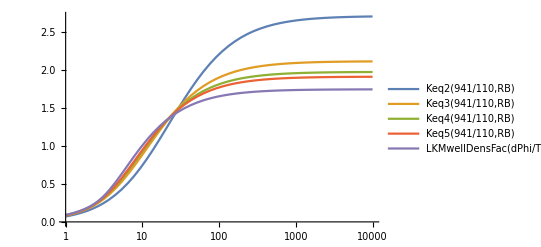

```mathematica
LogLinearPlot[{Keq2[941/110,RB],Keq3[941/110,RB],Keq4[941/110,RB],Keq5[941/110,RB],LKMwellDensFac[dPhi/Tm,RB]},{RB,1,10000},PlotLegends->"Expressions"]
```

```mathematica
Clear[Keq2]
```